# Scalar Field Thy Test

Init

```mathematica
Needs["QCDLib`"];
Needs["ErrorBarPlots`"];
```

M2=0.1, L=100

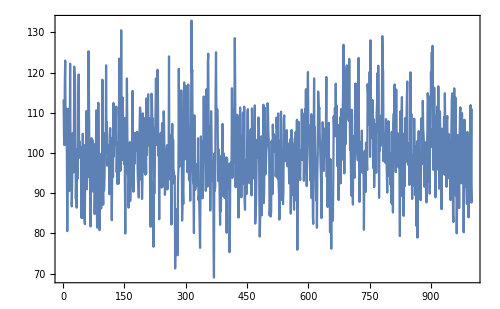

```mathematica
ListPlot[readRel["msq0.1_N1000_100.S.dat", "Real64"], Joined->True, frameOpts[]]
```

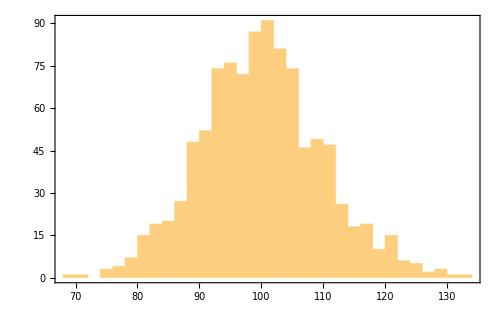

```mathematica
Histogram[readRel["msq0.1_N1000_100.S.dat", "Real64"], frameOpts[]]
```

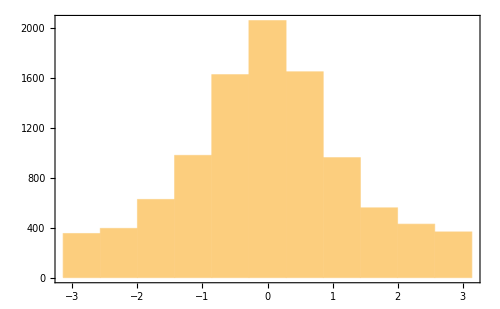

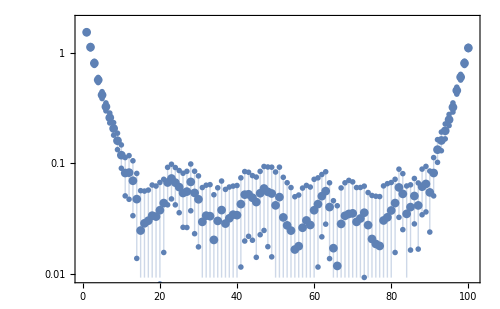

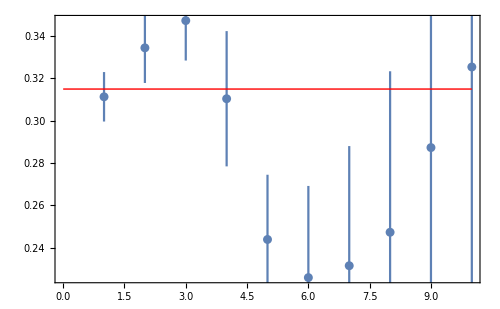

```mathematica
Module[{corrRaw, Nboot, Ncfg, Lt, Nsrc, corr, corrErr, mass, massErr, Mthy},
Ncfg = 1000;
Lt = 100;
Nsrc = 10;
Nboot = 500;
corrRaw = arrayReshape[
readRel["msq0.1_N1000_100.twopt.dat", "Complex128"],
{Ncfg, Lt, Nsrc}];
corrRaw = Transpose[corrRaw, {1,3,2}];
Print@Histogram[Arg@Flatten[corrRaw,1]⟦All,3⟧, {-Pi, Pi, 2 Pi/11}, frameOpts[]];
corrRaw = Total[corrRaw, {2}] / Nsrc;
{corr, corrErr} = bootstrap[Re@corrRaw, Nboot, Mean, "BinSize"->20];
{mass, massErr} = bootstrap[Re@corrRaw, Nboot, meff, "BinSize"->20];
Print@errorListLogPlot[Transpose@{corr, corrErr}, frameOpts[]];
Mthy = 2 ArcSinh[Sqrt[0.1] / 2];
Print@ErrorListPlot[Transpose[{mass, massErr}]⟦;;10⟧, frameOpts[],
Epilog->{Thick, Red, Line[{{0, Mthy}, {10, Mthy}}]}];
];
```

M2=0.1, L = 8

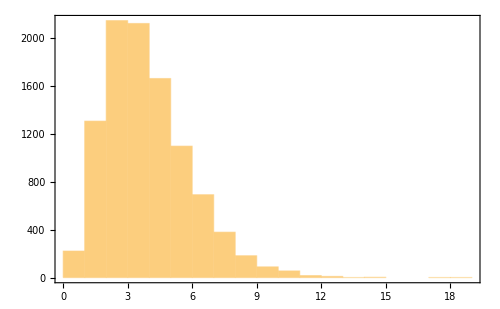

```mathematica
Histogram[readRel["msq0.1_N10000_8.S.dat", "Real64"], frameOpts[]]
```

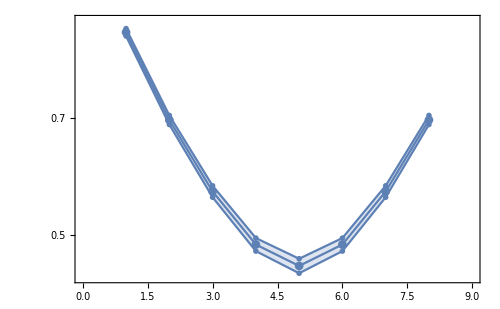

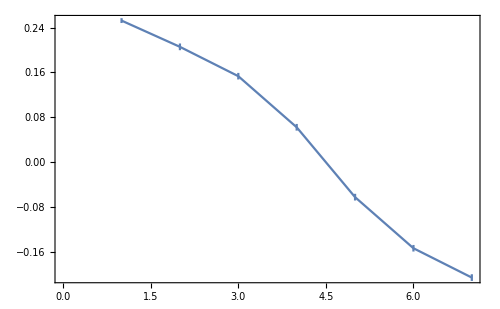

```mathematica
l8Meffs = Module[{corrRaw, Nboot, Ncfg, Lt, Nsrc, corr, corrErr, mass, massErr, Mthy, plt},
Ncfg = 10000;
Lt = 8;
Nboot = 500;
corrRaw = arrayReshape[
readRel["msq0.1_N10000_8.twopt.dat", "Complex128"],
{Ncfg, Lt}];
{corr, corrErr} = bootstrap[Re@corrRaw, Nboot, Mean, "BinSize"->20];
{mass, massErr} = bootstrap[Re@corrRaw, Nboot, meff, "BinSize"->20];
Print@errorListLogPlot[Transpose@{corr, corrErr}, frameOpts[],
Joined->True];
Mthy = 2 ArcSinh[Sqrt[0.1] / 2];
plt = ErrorListPlot[Transpose[{mass, massErr}], frameOpts[],
Epilog->{Thick, Red, Line[{{0, Mthy}, {10, Mthy}}]},
Joined->True];
Print@plt;
plt
];
```

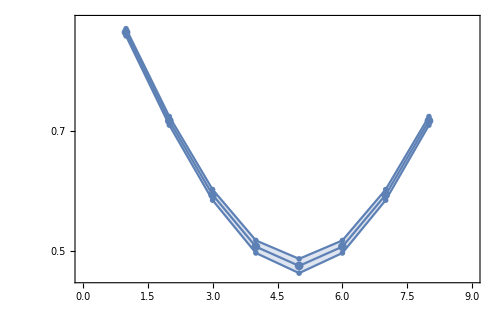

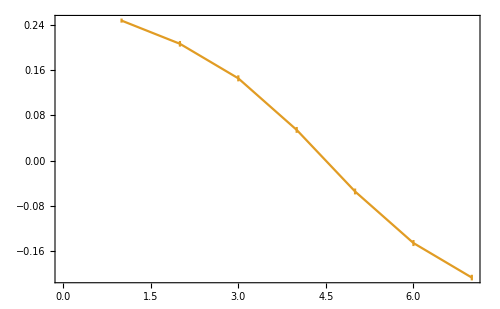

```mathematica
l8MeffsTake2 = Module[{corrRaw, Nboot, Ncfg, Lt, Nsrc, corr, corrErr, mass, massErr, Mthy, plt},
Ncfg = 10000;
Lt = 8;
Nboot = 500;
corrRaw = arrayReshape[
readRel["msq0.1_N10000_8_take2.twopt.dat", "Complex128"],
{Ncfg, Lt}];
{corr, corrErr} = bootstrap[Re@corrRaw, Nboot, Mean, "BinSize"->20];
{mass, massErr} = bootstrap[Re@corrRaw, Nboot, meff, "BinSize"->20];
Print@errorListLogPlot[Transpose@{corr, corrErr}, frameOpts[],
Joined->True];
Mthy = 2 ArcSinh[Sqrt[0.1] / 2];
plt = ErrorListPlot[Transpose[{mass, massErr}], frameOpts[],
Epilog->{Thick, Red, Line[{{0, Mthy}, {10, Mthy}}]},
Joined->True, PlotStyle->mmaColors⟦2⟧];
Print@plt;
plt
];
```

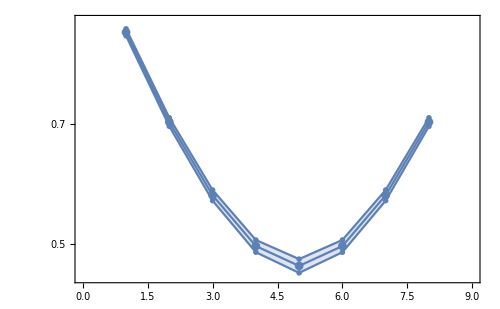

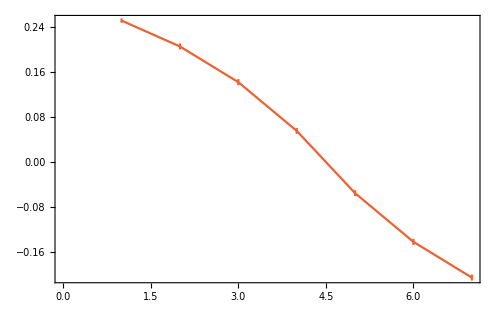

```mathematica
l8MeffsTake3 = Module[{corrRaw, Nboot, Ncfg, Lt, Nsrc, corr, corrErr, mass, massErr, Mthy, plt},
Ncfg = 10000;
Lt = 8;
Nboot = 500;
corrRaw = arrayReshape[
readRel["msq0.1_N10000_8_take3.twopt.dat", "Complex128"],
{Ncfg, Lt}];
{corr, corrErr} = bootstrap[Re@corrRaw, Nboot, Mean, "BinSize"->20];
{mass, massErr} = bootstrap[Re@corrRaw, Nboot, meff, "BinSize"->20];
Print@errorListLogPlot[Transpose@{corr, corrErr}, frameOpts[],
Joined->True];
Mthy = 2 ArcSinh[Sqrt[0.1] / 2];
plt = ErrorListPlot[Transpose[{mass, massErr}], frameOpts[],
Epilog->{Thick, Red, Line[{{0, Mthy}, {10, Mthy}}]},
Joined->True, PlotStyle->mmaColors⟦4⟧];
Print@plt;
plt
];
```

```mathematica
l8NNMeffs = ErrorListPlot[
Transpose@{{0.2525778,   0.20744684,  0.1367569,   0.04635011, -0.04635011, -0.1367569,
 -0.20744684},{0.00284319, 0.00374041, 0.00425899, 0.00279706, 0.00279706, 0.00425899,
 0.00374042}}, frameOpts[], Joined->True,
PlotStyle->mmaColors⟦3⟧];
```

```mathematica
Rasterize@Legended[Show[l8Meffs, l8MeffsTake2, l8MeffsTake3, l8NNMeffs,
PlotLabel->title["8-site scalar meff"]],
SwatchLegend[{mmaColors⟦1⟧, mmaColors⟦2⟧, mmaColors⟦4⟧, mmaColors⟦3⟧},
title/@{"HMC1", "HMC2", "HMC3", "NN generated"}]]
```